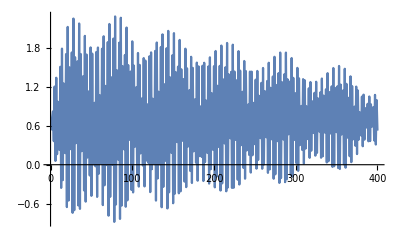

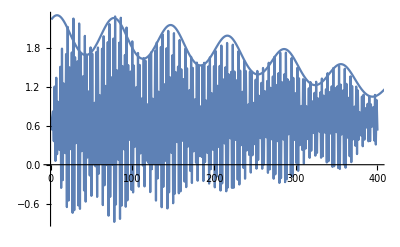

```mathematica
filter=Import["C:\\Users\\Расим\\Desktop\\Filter.txt","Table"];
filter1=Table[filter[[n,2]],{n,1,400}];
ListLinePlot[filter1]
Show[ListLinePlot[filter1],Plot[2.3*Exp[-(x)^2/(2*400^2)]*Exp[-0.39^2*(1-Cos[0.09*(x-8)])],{x,1,1000}]]
```

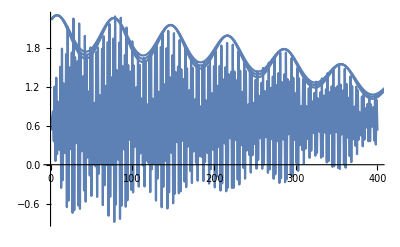

```mathematica
Show[ListLinePlot[filter1],Plot[2.3*Exp[-(x)^2/(2*400^2)]*Exp[-0.39^2*(1-Cos[0.09*(x-8)])],{x,1,1000}],Plot[2.3*Exp[-(x)^2/(2*400^2)]*Exp[-0.37^2*(1-Cos[0.09*(x-8)])],{x,1,1000}],Plot[2.3*Exp[-(x)^2/(2*400^2)]*Exp[-0.41^2*(1-Cos[0.09*(x-8)])],{x,1,1000}]]
```